```mathematica
data=
Transpose[Import["C:\\Users\\Abigail\\Desktop\\Wolfram data\\Nematode\\Data_nematode.csv"]];
hdr=data//First
```

{Classification,Species,Species,Species,Species,Species,Species,Species,Species,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Genus,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Family,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order,Order}

```mathematica
Dimensions[data]
```

{7,122}

```mathematica
nematode12S=data[[2,2;;122]]
nematode16S=data[[3,2;;122]]
nematodeCOI=data[[4,2;;122]]
nematodeCOII=data[[5,2;;122]]
nematodecytb=data[[6,2;;122]]
nematodeND=data[[7,2;;122]]
```

{0,0,0.02,0.02,0,0.014,0.052,0.055,0.063,0.063,0.075,0.063,0.063,0.075,0.084,0.084,0.115,0.089,0.11,0.081,0.104,0.092,0.101,0.107,0.098,0.118,0.104,0.104,0.11,0.107,0.098,0.118,0.104,0.104,0.11,0.101,0.098,0.121,0.089,0.089,0.104,0.101,0.098,0.121,0.089,0.089,0.104,0.107,0.104,0.127,0.107,0.107,0.121,0.098,0.098,0.112,0.297,0.297,0.277,0.294,0.288,0.291,0.297,0.297,0.277,0.294,0.288,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.294,0.285,0.294,0.294,0.285,0.288,0.282,0.291,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.294,0.291,0.282,0.271,0.288,0.314,0.303,0.303,0.308,0.311,0.311,0.308,0.334,0.329,0.343,0.334,0.334}

{0.015,0.008,0.005,0.007,0.002,0.013,0.06,0.06,0.079,0.084,0.081,0.094,0.099,0.096,0.187,0.187,0.109,0.121,0.111,0.119,0.103,0.118,0.109,0.174,0.161,0.179,0.204,0.202,0.197,0.185,0.172,0.19,0.215,0.214,0.209,0.154,0.149,0.162,0.19,0.19,0.179,0.159,0.156,0.169,0.197,0.197,0.185,0.157,0.154,0.167,0.194,0.194,0.182,0.172,0.172,0.189,0.293,0.296,0.301,0.3,0.298,0.285,0.301,0.305,0.31,0.311,0.306,0.293,0.29,0.293,0.298,0.301,0.3,0.28,0.296,0.3,0.305,0.308,0.306,0.286,0.295,0.298,0.303,0.306,0.305,0.28,0.31,0.311,0.311,0.318,0.318,0.29,0.313,0.316,0.316,0.316,0.308,0.298,0.311,0.315,0.315,0.315,0.306,0.296,0.295,0.296,0.293,0.295,0.296,0.278,0.301,0.303,0.31,0.301,0.301,0.306,0.311,0.316,0.318,0.323,0.315}

{0.002,0.003,0.002,0.005,0.008,0.025,0.083,0.084,0.094,0.097,0.095,0.097,0.099,0.097,0.158,0.159,0.117,0.12,0.113,0.12,0.114,0.123,0.111,0.13,0.128,0.123,0.15,0.152,0.151,0.132,0.13,0.125,0.15,0.152,0.153,0.112,0.117,0.109,0.133,0.135,0.131,0.12,0.112,0.136,0.137,0.131,0.179,0.109,0.135,0.137,0.131,0.177,0.173,0.143,0.191,0.188,0.315,0.315,0.324,0.321,0.328,0.19,0.315,0.315,0.323,0.32,0.328,0.192,0.3,0.304,0.314,0.308,0.319,0.169,0.3,0.304,0.313,0.31,0.32,0.171,0.299,0.303,0.313,0.307,0.319,0.169,0.316,0.319,0.331,0.322,0.332,0.194,0.322,0.328,0.325,0.315,0.326,0.199,0.323,0.328,0.327,0.32,0.328,0.199,0.328,0.328,0.338,0.335,0.339,0.199,0.343,0.341,0.337,0.343,0.35,0.22,0.318,0.319,0.318,0.315,0.326}

{0.002,0.005,0,0.005,0.002,0.04,0.103,0.096,0.087,0.085,0.087,0.085,0.083,0.085,0.152,0.154,0.139,0.15,0.139,0.149,0.132,0.149,0.149,0.138,0.112,0.125,0.147,0.149,0.167,0.136,0.111,0.123,0.147,0.149,0.167,0.13,0.118,0.123,0.152,0.154,0.156,0.134,0.118,0.123,0.149,0.15,0.152,0.13,0.118,0.123,0.152,0.154,0.156,0.149,0.15,0.152,0.389,0.391,0.388,0.422,0.389,0.426,0.388,0.389,0.386,0.42,0.389,0.424,0.38,0.4,0.373,0.409,0.388,0.395,0.382,0.402,0.377,0.408,0.386,0.393,0.38,0.4,0.373,0.409,0.388,0.395,0.4,0.399,0.389,0.415,0.395,0.417,0.388,0.388,0.373,0.402,0.389,0.428,0.389,0.389,0.371,0.402,0.391,0.429,0.391,0.406,0.402,0.413,0.391,0.413,0.114,0.1,0.096,0.139,0.149,0.232,0.248,0.248,0.239,0.223,0.252}

{0.001,0.001,0.021,0.02,0.019,0.037,0.099,0.092,0.151,0.15,0.164,0.152,0.151,0.165,0.216,0.22,0.122,0.138,0.115,0.136,0.117,0.127,0.14,0.215,0.204,0.219,0.229,0.227,0.233,0.216,0.205,0.22,0.23,0.228,0.234,0.197,0.185,0.204,0.223,0.223,0.235,0.196,0.185,0.203,0.222,0.222,0.234,0.209,0.199,0.216,0.232,0.232,0.247,0.216,0.22,0.241,0.33,0.325,0.335,0.344,0.335,0.343,0.331,0.326,0.336,0.345,0.336,0.344,0.345,0.33,0.33,0.338,0.329,0.336,0.344,0.329,0.329,0.337,0.328,0.335,0.35,0.338,0.337,0.347,0.338,0.345,0.357,0.348,0.358,0.372,0.372,0.362,0.349,0.348,0.337,0.353,0.345,0.369,0.351,0.354,0.341,0.36,0.346,0.373,0.347,0.34,0.337,0.338,0.346,0.364,0.127,0.125,0.135,0.149,0.158,0.209,0.199,0.189,0.18,0.201,0.205}

{0.001,0.001,0.006,0.005,0.041,0.102,0.095,0.006,0.132,0.131,0.136,0.133,0.132,0.137,0.189,0.19,0.143,0.171,0.138,0.175,0.142,0.152,0.148,0.174,0.166,0.17,0.175,0.179,0.166,0.175,0.168,0.171,0.176,0.18,0.168,0.155,0.155,0.168,0.157,0.161,0.174,0.154,0.154,0.166,0.156,0.16,0.173,0.156,0.156,0.169,0.161,0.165,0.178,0.159,0.162,0.185,0.346,0.346,0.343,0.344,0.32,0.321,0.348,0.348,0.344,0.345,0.321,0.322,0.326,0.319,0.33,0.334,0.312,0.315,0.325,0.317,0.329,0.332,0.311,0.313,0.327,0.32,0.331,0.336,0.313,0.319,0.343,0.338,0.343,0.35,0.338,0.339,0.355,0.345,0.338,0.363,0.34,0.322,0.359,0.349,0.341,0.367,0.344,0.326,0.336,0.334,0.341,0.352,0.339,0.32,0.156,0.147,0.136,0.151,0.168,0.203,0.22,0.208,0.202,0.216,0.227}

```mathematica
Stat[clusterdata_]:={Mean[#],StandardDeviation[#],MinMax[#]}&/@clusterdata
```

```mathematica
PlotCluster[clusterdata_,plotlabel_]:=ListPlot[clusterdata,BaseStyle->{FontFamily->"Times New Roman",FontSize->12},Frame->True,FrameLabel->{"Samples","Genetic Distance"},GridLines->Automatic,ImageSize->Medium,PlotStyle->{{PointSize[Medium],Red},{PointSize[Medium],Green},{PointSize[Medium],Blue},{PointSize[Medium],Orange}},PlotLabel->plotlabel]
```

```mathematica
{clstrnematode12S,clstrnematode16S,clstrnematodeCOI,clstrnematodeCOII,clstrnematodecytb,clstrnematodeND}=FindClusters[#,4,Method->"KMeans"]&/@{nematode12S,nematode16S,nematodeCOI,nematodeCOII,nematodecytb,nematodeND};
```

```mathematica
Stat[clstrnematode12S]
```

{{0.009,0.0100995,{0,0.02}},{0.0751875,0.0133727,{0.052,0.089}},{0.106853,0.00823199,{0.092,0.127}},{0.293431,0.0158784,{0.268,0.343}}}

```mathematica
statdata=Stat/@{clstrnematode12S,clstrnematode16S,clstrnematodeCOI,clstrnematodeCOII,clstrnematodecytb,clstrnematodeND}
```

{{{0.009,0.0100995,{0,0.02}},{0.0751875,0.0133727,{0.052,0.089}},{0.106853,0.00823199,{0.092,0.127}},{0.293431,0.0158784,{0.268,0.343}}},{{0.02125,0.0242708,{0.002,0.06}},{0.101769,0.0144,{0.079,0.121}},{0.181257,0.0180544,{0.149,0.215}},{0.302923,0.0101724,{0.278,0.323}}},{{0.0075,0.0088713,{0.002,0.025}},{0.122512,0.0188798,{0.083,0.153}},{0.183941,0.0164904,{0.158,0.22}},{0.3214,0.0115142,{0.299,0.35}}},{{0.0600625,0.042175,{0,0.103}},{0.152373,0.0354965,{0.111,0.252}},{0.38925,0.00839337,{0.371,0.402}},{0.417071,0.00781974,{0.406,0.429}}},{{0.0165,0.0137077,{0.001,0.037}},{0.13565,0.0202414,{0.092,0.165}},{0.215122,0.0162253,{0.18,0.247}},{0.343741,0.0122107,{0.325,0.373}}},{{0.01,0.0153623,{0.001,0.041}},{0.156385,0.0181898,{0.095,0.18}},{0.204444,0.0147064,{0.185,0.227}},{0.334796,0.0137311,{0.311,0.367}}}}

```mathematica
MySort[clusterdata_]:=Module[{len,max,or},
len=Length@clusterdata;
max=Max/@clusterdata;
or=Ordering[max];
clusterdata[[or]]
];
```

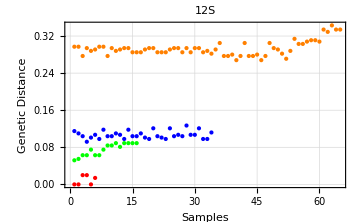

```mathematica
PlotCluster[MySort[clstrnematode12S],"12S"]
```

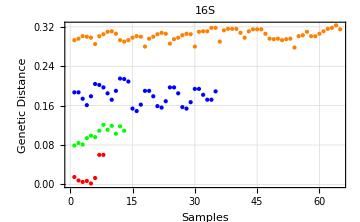

```mathematica
PlotCluster[MySort[clstrnematode16S],"16S"]
```

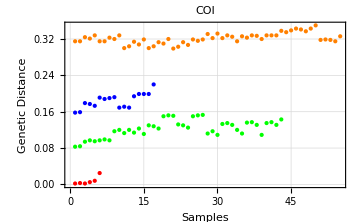

```mathematica
PlotCluster[MySort[clstrnematodeCOI],"COI"]
```

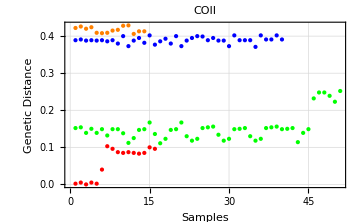

```mathematica
PlotCluster[MySort[clstrnematodeCOII],"COII"]
```

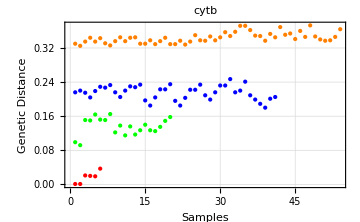

```mathematica
PlotCluster[MySort[clstrnematodecytb],"cytb"]
```

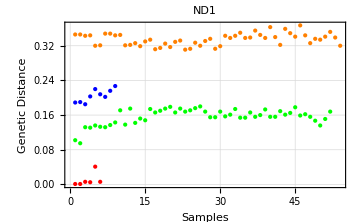

```mathematica
PlotCluster[MySort[clstrnematodeND],"ND1"]
```

```mathematica
Mean[nematode12S]
```

0.198041

```mathematica
FindClusters[nematode12S,4,Method->"KMeans"]
```

{{0,0,0.02,0.02,0,0.014},{0.052,0.055,0.063,0.063,0.075,0.063,0.063,0.075,0.084,0.084,0.089,0.081,0.089,0.089,0.089,0.089},{0.115,0.11,0.104,0.092,0.101,0.107,0.098,0.118,0.104,0.104,0.11,0.107,0.098,0.118,0.104,0.104,0.11,0.101,0.098,0.121,0.104,0.101,0.098,0.121,0.104,0.107,0.104,0.127,0.107,0.107,0.121,0.098,0.098,0.112},{0.297,0.297,0.277,0.294,0.288,0.291,0.297,0.297,0.277,0.294,0.288,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.294,0.285,0.294,0.294,0.285,0.288,0.282,0.291,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.294,0.291,0.282,0.271,0.288,0.314,0.303,0.303,0.308,0.311,0.311,0.308,0.334,0.329,0.343,0.334,0.334}}

```mathematica
Mean[{0,0,0.02,0.02,0,0.014}]
```

0.009

```mathematica
StandardDeviation[{0,0,0.02,0.02,0,0.014}]
```

0.0100995

```mathematica
Mean[{0.052,0.055,0.063,0.063,0.075,0.063,0.063,0.075,0.084,0.084,0.089,0.081,0.089,0.089,0.089,0.089}]
```

0.0751875

```mathematica
StandardDeviation[{0.052,0.055,0.063,0.063,0.075,0.063,0.063,0.075,0.084,0.084,0.089,0.081,0.089,0.089,0.089,0.089}]
```

0.0133727

```mathematica
Mean[{0.115,0.11,0.104,0.092,0.101,0.107,0.098,0.118,0.104,0.104,0.11,0.107,0.098,0.118,0.104,0.104,0.11,0.101,0.098,0.121,0.104,0.101,0.098,0.121,0.104,0.107,0.104,0.127,0.107,0.107,0.121,0.098,0.098,0.112}]
```

0.106853

```mathematica
StandardDeviation[{0.115,0.11,0.104,0.092,0.101,0.107,0.098,0.118,0.104,0.104,0.11,0.107,0.098,0.118,0.104,0.104,0.11,0.101,0.098,0.121,0.104,0.101,0.098,0.121,0.104,0.107,0.104,0.127,0.107,0.107,0.121,0.098,0.098,0.112}]
```

0.00823199

```mathematica
Mean[{0.297,0.297,0.277,0.294,0.288,0.291,0.297,0.297,0.277,0.294,0.288,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.294,0.285,0.294,0.294,0.285,0.288,0.282,0.291,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.294,0.291,0.282,0.271,0.288,0.314,0.303,0.303,0.308,0.311,0.311,0.308,0.334,0.329,0.343,0.334,0.334}]
```

0.293431

```mathematica
StandardDeviation[{0.297,0.297,0.277,0.294,0.288,0.291,0.297,0.297,0.277,0.294,0.288,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.285,0.285,0.291,0.294,0.294,0.285,0.294,0.285,0.294,0.294,0.285,0.288,0.282,0.291,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.277,0.277,0.28,0.268,0.277,0.305,0.294,0.291,0.282,0.271,0.288,0.314,0.303,0.303,0.308,0.311,0.311,0.308,0.334,0.329,0.343,0.334,0.334}]
```

0.0158784

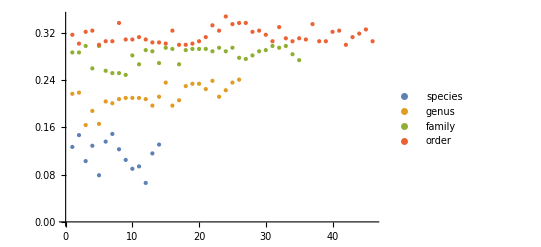

```mathematica
ListPlot[FindClusters[nematode12S,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
FindClusters[nematode16S,4,Method->"KMeans"]
```

{{0.015,0.008,0.005,0.007,0.002,0.013,0.06,0.06},{0.079,0.084,0.081,0.094,0.099,0.096,0.109,0.121,0.111,0.119,0.103,0.118,0.109},{0.187,0.187,0.174,0.161,0.179,0.204,0.202,0.197,0.185,0.172,0.19,0.215,0.214,0.209,0.154,0.149,0.162,0.19,0.19,0.179,0.159,0.156,0.169,0.197,0.197,0.185,0.157,0.154,0.167,0.194,0.194,0.182,0.172,0.172,0.189},{0.293,0.296,0.301,0.3,0.298,0.285,0.301,0.305,0.31,0.311,0.306,0.293,0.29,0.293,0.298,0.301,0.3,0.28,0.296,0.3,0.305,0.308,0.306,0.286,0.295,0.298,0.303,0.306,0.305,0.28,0.31,0.311,0.311,0.318,0.318,0.29,0.313,0.316,0.316,0.316,0.308,0.298,0.311,0.315,0.315,0.315,0.306,0.296,0.295,0.296,0.293,0.295,0.296,0.278,0.301,0.303,0.31,0.301,0.301,0.306,0.311,0.316,0.318,0.323,0.315}}

```mathematica
Mean[{0.015,0.008,0.005,0.007,0.002,0.013,0.06,0.06}]
```

0.02125

```mathematica
StandardDeviation[{0.015,0.008,0.005,0.007,0.002,0.013,0.06,0.06}]
```

0.0242708

```mathematica
Mean[{0.079,0.084,0.081,0.094,0.099,0.096,0.109,0.121,0.111,0.119,0.103,0.118,0.109}]
```

0.101769

```mathematica
StandardDeviation[{0.079,0.084,0.081,0.094,0.099,0.096,0.109,0.121,0.111,0.119,0.103,0.118,0.109}]
```

0.0144

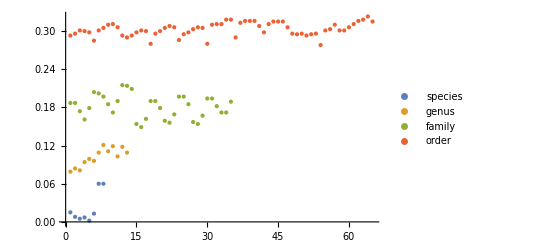

```mathematica
ListPlot[FindClusters[nematode16S,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
FindClusters[nematodeCOI,4,Method->"KMeans"]
```

{{0.002,0.003,0.002,0.005,0.008,0.025},{0.083,0.084,0.094,0.097,0.095,0.097,0.099,0.097,0.117,0.12,0.113,0.12,0.114,0.123,0.111,0.13,0.128,0.123,0.15,0.152,0.151,0.132,0.13,0.125,0.15,0.152,0.153,0.112,0.117,0.109,0.133,0.135,0.131,0.12,0.112,0.136,0.137,0.131,0.109,0.135,0.137,0.131,0.143},{0.158,0.159,0.179,0.177,0.173,0.191,0.188,0.19,0.192,0.169,0.171,0.169,0.194,0.199,0.199,0.199,0.22},{0.315,0.315,0.324,0.321,0.328,0.315,0.315,0.323,0.32,0.328,0.3,0.304,0.314,0.308,0.319,0.3,0.304,0.313,0.31,0.32,0.299,0.303,0.313,0.307,0.319,0.316,0.319,0.331,0.322,0.332,0.322,0.328,0.325,0.315,0.326,0.323,0.328,0.327,0.32,0.328,0.328,0.328,0.338,0.335,0.339,0.343,0.341,0.337,0.343,0.35,0.318,0.319,0.318,0.315,0.326}}

```mathematica
Mean[{0.002,0.003,0.002,0.005,0.008,0.025}]
```

0.0075

```mathematica
StandardDeviation[{0.002,0.003,0.002,0.005,0.008,0.025}]
```

0.0088713

```mathematica
Mean[{0.083,0.084,0.094,0.097,0.095,0.097,0.099,0.097,0.117,0.12,0.113,0.12,0.114,0.123,0.111,0.13,0.128,0.123,0.15,0.152,0.151,0.132,0.13,0.125,0.15,0.152,0.153,0.112,0.117,0.109,0.133,0.135,0.131,0.12,0.112,0.136,0.137,0.131,0.109,0.135,0.137,0.131,0.143}]
```

0.122512

```mathematica
StandardDeviation[{0.083,0.084,0.094,0.097,0.095,0.097,0.099,0.097,0.117,0.12,0.113,0.12,0.114,0.123,0.111,0.13,0.128,0.123,0.15,0.152,0.151,0.132,0.13,0.125,0.15,0.152,0.153,0.112,0.117,0.109,0.133,0.135,0.131,0.12,0.112,0.136,0.137,0.131,0.109,0.135,0.137,0.131,0.143}]
```

0.0188798

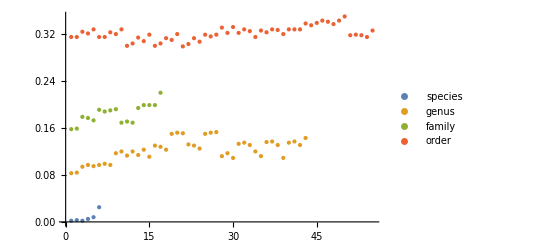

```mathematica
ListPlot[FindClusters[nematodeCOI,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
Mean[{0.158,0.159,0.179,0.177,0.173,0.191,0.188,0.19,0.192,0.169,0.171,0.169,0.194,0.199,0.199,0.199,0.22}]
```

0.183941

```mathematica
StandardDeviation[{0.158,0.159,0.179,0.177,0.173,0.191,0.188,0.19,0.192,0.169,0.171,0.169,0.194,0.199,0.199,0.199,0.22}]
```

0.0164904

```mathematica
Mean[{0.315,0.315,0.324,0.321,0.328,0.315,0.315,0.323,0.32,0.328,0.3,0.304,0.314,0.308,0.319,0.3,0.304,0.313,0.31,0.32,0.299,0.303,0.313,0.307,0.319,0.316,0.319,0.331,0.322,0.332,0.322,0.328,0.325,0.315,0.326,0.323,0.328,0.327,0.32,0.328,0.328,0.328,0.338,0.335,0.339,0.343,0.341,0.337,0.343,0.35,0.318,0.319,0.318,0.315,0.326}]
```

0.3214

```mathematica
StandardDeviation[{0.315,0.315,0.324,0.321,0.328,0.315,0.315,0.323,0.32,0.328,0.3,0.304,0.314,0.308,0.319,0.3,0.304,0.313,0.31,0.32,0.299,0.303,0.313,0.307,0.319,0.316,0.319,0.331,0.322,0.332,0.322,0.328,0.325,0.315,0.326,0.323,0.328,0.327,0.32,0.328,0.328,0.328,0.338,0.335,0.339,0.343,0.341,0.337,0.343,0.35,0.318,0.319,0.318,0.315,0.326}]
```

0.0115142

```mathematica
FindClusters[nematodeCOII,4,Method->"KMeans"]
```

{{0.002,0.005,0,0.005,0.002,0.04,0.103,0.096,0.087,0.085,0.087,0.085,0.083,0.085,0.1,0.096},{0.152,0.154,0.139,0.15,0.139,0.149,0.132,0.149,0.149,0.138,0.112,0.125,0.147,0.149,0.167,0.136,0.111,0.123,0.147,0.149,0.167,0.13,0.118,0.123,0.152,0.154,0.156,0.134,0.118,0.123,0.149,0.15,0.152,0.13,0.118,0.123,0.152,0.154,0.156,0.149,0.15,0.152,0.114,0.139,0.149,0.232,0.248,0.248,0.239,0.223,0.252},{0.389,0.391,0.388,0.389,0.388,0.389,0.386,0.389,0.38,0.4,0.373,0.388,0.395,0.382,0.402,0.377,0.386,0.393,0.38,0.4,0.373,0.388,0.395,0.4,0.399,0.389,0.395,0.388,0.388,0.373,0.402,0.389,0.389,0.389,0.371,0.402,0.391,0.391,0.402,0.391},{0.422,0.426,0.42,0.424,0.409,0.408,0.409,0.415,0.417,0.428,0.429,0.406,0.413,0.413}}

```mathematica
Mean[{0.002,0.005,0,0.005,0.002,0.04,0.103,0.096,0.087,0.085,0.087,0.085,0.083,0.085,0.1,0.096}]
```

0.0600625

```mathematica
StandardDeviation[{0.002,0.005,0,0.005,0.002,0.04,0.103,0.096,0.087,0.085,0.087,0.085,0.083,0.085,0.1,0.096}]
```

0.042175

```mathematica
Mean[{0.152,0.154,0.139,0.15,0.139,0.149,0.132,0.149,0.149,0.138,0.112,0.125,0.147,0.149,0.167,0.136,0.111,0.123,0.147,0.149,0.167,0.13,0.118,0.123,0.152,0.154,0.156,0.134,0.118,0.123,0.149,0.15,0.152,0.13,0.118,0.123,0.152,0.154,0.156,0.149,0.15,0.152,0.114,0.139,0.149,0.232,0.248,0.248,0.239,0.223,0.252}]
```

0.152373

```mathematica
StandardDeviation[{0.152,0.154,0.139,0.15,0.139,0.149,0.132,0.149,0.149,0.138,0.112,0.125,0.147,0.149,0.167,0.136,0.111,0.123,0.147,0.149,0.167,0.13,0.118,0.123,0.152,0.154,0.156,0.134,0.118,0.123,0.149,0.15,0.152,0.13,0.118,0.123,0.152,0.154,0.156,0.149,0.15,0.152,0.114,0.139,0.149,0.232,0.248,0.248,0.239,0.223,0.252}]
```

0.0354965

```mathematica
Mean[{0.389,0.391,0.388,0.389,0.388,0.389,0.386,0.389,0.38,0.4,0.373,0.388,0.395,0.382,0.402,0.377,0.386,0.393,0.38,0.4,0.373,0.388,0.395,0.4,0.399,0.389,0.395,0.388,0.388,0.373,0.402,0.389,0.389,0.389,0.371,0.402,0.391,0.391,0.402,0.391}]
```

0.38925

```mathematica
StandardDeviation[{0.389,0.391,0.388,0.389,0.388,0.389,0.386,0.389,0.38,0.4,0.373,0.388,0.395,0.382,0.402,0.377,0.386,0.393,0.38,0.4,0.373,0.388,0.395,0.4,0.399,0.389,0.395,0.388,0.388,0.373,0.402,0.389,0.389,0.389,0.371,0.402,0.391,0.391,0.402,0.391}]
```

0.00839337

```mathematica
Mean[{0.422,0.426,0.42,0.424,0.409,0.408,0.409,0.415,0.417,0.428,0.429,0.406,0.413,0.413}]
```

0.417071

```mathematica
StandardDeviation[{0.422,0.426,0.42,0.424,0.409,0.408,0.409,0.415,0.417,0.428,0.429,0.406,0.413,0.413}]
```

0.00781974

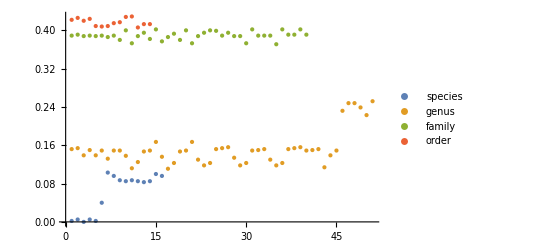

```mathematica
ListPlot[FindClusters[nematodeCOII,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
ListPlot[FindClusters[nematodeCOII,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

-Graphics-

```mathematica
FindClusters[nematodecytb,4,Method->"KMeans"]
```

{{0.001,0.001,0.021,0.02,0.019,0.037},{0.099,0.092,0.151,0.15,0.164,0.152,0.151,0.165,0.122,0.138,0.115,0.136,0.117,0.127,0.14,0.127,0.125,0.135,0.149,0.158},{0.216,0.22,0.215,0.204,0.219,0.229,0.227,0.233,0.216,0.205,0.22,0.23,0.228,0.234,0.197,0.185,0.204,0.223,0.223,0.235,0.196,0.185,0.203,0.222,0.222,0.234,0.209,0.199,0.216,0.232,0.232,0.247,0.216,0.22,0.241,0.209,0.199,0.189,0.18,0.201,0.205},{0.33,0.325,0.335,0.344,0.335,0.343,0.331,0.326,0.336,0.345,0.336,0.344,0.345,0.33,0.33,0.338,0.329,0.336,0.344,0.329,0.329,0.337,0.328,0.335,0.35,0.338,0.337,0.347,0.338,0.345,0.357,0.348,0.358,0.372,0.372,0.362,0.349,0.348,0.337,0.353,0.345,0.369,0.351,0.354,0.341,0.36,0.346,0.373,0.347,0.34,0.337,0.338,0.346,0.364}}

```mathematica
Mean[{0.001,0.001,0.021,0.02,0.019,0.037}]
```

0.0165

```mathematica
StandardDeviation[{0.001,0.001,0.021,0.02,0.019,0.037}]
```

0.0137077

```mathematica
Mean[{0.099,0.092,0.151,0.15,0.164,0.152,0.151,0.165,0.122,0.138,0.115,0.136,0.117,0.127,0.14,0.127,0.125,0.135,0.149,0.158}]
```

0.13565

```mathematica
StandardDeviation[{0.099,0.092,0.151,0.15,0.164,0.152,0.151,0.165,0.122,0.138,0.115,0.136,0.117,0.127,0.14,0.127,0.125,0.135,0.149,0.158}]
```

0.0202414

```mathematica
Mean[{0.216,0.22,0.215,0.204,0.219,0.229,0.227,0.233,0.216,0.205,0.22,0.23,0.228,0.234,0.197,0.185,0.204,0.223,0.223,0.235,0.196,0.185,0.203,0.222,0.222,0.234,0.209,0.199,0.216,0.232,0.232,0.247,0.216,0.22,0.241,0.209,0.199,0.189,0.18,0.201,0.205}]
```

0.215122

```mathematica
StandardDeviation[{0.216,0.22,0.215,0.204,0.219,0.229,0.227,0.233,0.216,0.205,0.22,0.23,0.228,0.234,0.197,0.185,0.204,0.223,0.223,0.235,0.196,0.185,0.203,0.222,0.222,0.234,0.209,0.199,0.216,0.232,0.232,0.247,0.216,0.22,0.241,0.209,0.199,0.189,0.18,0.201,0.205}]
```

0.0162253

```mathematica
Mean[{0.33,0.325,0.335,0.344,0.335,0.343,0.331,0.326,0.336,0.345,0.336,0.344,0.345,0.33,0.33,0.338,0.329,0.336,0.344,0.329,0.329,0.337,0.328,0.335,0.35,0.338,0.337,0.347,0.338,0.345,0.357,0.348,0.358,0.372,0.372,0.362,0.349,0.348,0.337,0.353,0.345,0.369,0.351,0.354,0.341,0.36,0.346,0.373,0.347,0.34,0.337,0.338,0.346,0.364}]
```

0.343741

```mathematica
StandardDeviation[{0.33,0.325,0.335,0.344,0.335,0.343,0.331,0.326,0.336,0.345,0.336,0.344,0.345,0.33,0.33,0.338,0.329,0.336,0.344,0.329,0.329,0.337,0.328,0.335,0.35,0.338,0.337,0.347,0.338,0.345,0.357,0.348,0.358,0.372,0.372,0.362,0.349,0.348,0.337,0.353,0.345,0.369,0.351,0.354,0.341,0.36,0.346,0.373,0.347,0.34,0.337,0.338,0.346,0.364}]
```

0.0122107

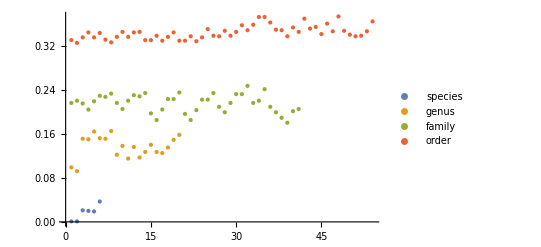

```mathematica
ListPlot[FindClusters[nematodecytb,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```

```mathematica
FindClusters[nematodeND,4,Method->"KMeans"]
```

{{0.001,0.001,0.006,0.005,0.041,0.006},{0.102,0.095,0.132,0.131,0.136,0.133,0.132,0.137,0.143,0.171,0.138,0.175,0.142,0.152,0.148,0.174,0.166,0.17,0.175,0.179,0.166,0.175,0.168,0.171,0.176,0.18,0.168,0.155,0.155,0.168,0.157,0.161,0.174,0.154,0.154,0.166,0.156,0.16,0.173,0.156,0.156,0.169,0.161,0.165,0.178,0.159,0.162,0.156,0.147,0.136,0.151,0.168},{0.189,0.19,0.185,0.203,0.22,0.208,0.202,0.216,0.227},{0.346,0.346,0.343,0.344,0.32,0.321,0.348,0.348,0.344,0.345,0.321,0.322,0.326,0.319,0.33,0.334,0.312,0.315,0.325,0.317,0.329,0.332,0.311,0.313,0.327,0.32,0.331,0.336,0.313,0.319,0.343,0.338,0.343,0.35,0.338,0.339,0.355,0.345,0.338,0.363,0.34,0.322,0.359,0.349,0.341,0.367,0.344,0.326,0.336,0.334,0.341,0.352,0.339,0.32}}

```mathematica
Mean[{0.001,0.001,0.006,0.005,0.041,0.006}]
```

0.01

```mathematica
StandardDeviation[{0.001,0.001,0.006,0.005,0.041,0.006}]
```

0.0153623

```mathematica
Mean[{0.102,0.095,0.132,0.131,0.136,0.133,0.132,0.137,0.143,0.171,0.138,0.175,0.142,0.152,0.148,0.174,0.166,0.17,0.175,0.179,0.166,0.175,0.168,0.171,0.176,0.18,0.168,0.155,0.155,0.168,0.157,0.161,0.174,0.154,0.154,0.166,0.156,0.16,0.173,0.156,0.156,0.169,0.161,0.165,0.178,0.159,0.162,0.156,0.147,0.136,0.151,0.168}]
```

0.156385

```mathematica
StandardDeviation[{0.102,0.095,0.132,0.131,0.136,0.133,0.132,0.137,0.143,0.171,0.138,0.175,0.142,0.152,0.148,0.174,0.166,0.17,0.175,0.179,0.166,0.175,0.168,0.171,0.176,0.18,0.168,0.155,0.155,0.168,0.157,0.161,0.174,0.154,0.154,0.166,0.156,0.16,0.173,0.156,0.156,0.169,0.161,0.165,0.178,0.159,0.162,0.156,0.147,0.136,0.151,0.168}]
```

0.0181898

```mathematica
Mean[{0.189,0.19,0.185,0.203,0.22,0.208,0.202,0.216,0.227}]
```

0.204444

```mathematica
StandardDeviation[{0.189,0.19,0.185,0.203,0.22,0.208,0.202,0.216,0.227}]
```

0.0147064

```mathematica
Mean[{0.346,0.346,0.343,0.344,0.32,0.321,0.348,0.348,0.344,0.345,0.321,0.322,0.326,0.319,0.33,0.334,0.312,0.315,0.325,0.317,0.329,0.332,0.311,0.313,0.327,0.32,0.331,0.336,0.313,0.319,0.343,0.338,0.343,0.35,0.338,0.339,0.355,0.345,0.338,0.363,0.34,0.322,0.359,0.349,0.341,0.367,0.344,0.326,0.336,0.334,0.341,0.352,0.339,0.32}]
```

0.334796

```mathematica
StandardDeviation[{0.346,0.346,0.343,0.344,0.32,0.321,0.348,0.348,0.344,0.345,0.321,0.322,0.326,0.319,0.33,0.334,0.312,0.315,0.325,0.317,0.329,0.332,0.311,0.313,0.327,0.32,0.331,0.336,0.313,0.319,0.343,0.338,0.343,0.35,0.338,0.339,0.355,0.345,0.338,0.363,0.34,0.322,0.359,0.349,0.341,0.367,0.344,0.326,0.336,0.334,0.341,0.352,0.339,0.32}]
```

0.0137311

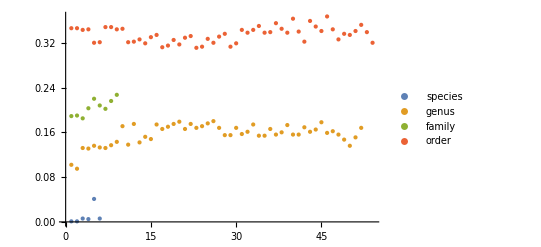

```mathematica
ListPlot[FindClusters[nematodeND,4,Method->"KMeans"],PlotLegends->{species,genus,family,order},PlotStyle->PointSize[Medium],BaseStyle->{FontFamily->"Times New Roman",FontSize->12}]
```